```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/leima/GitHub/NeuPhysics/aNN/MMA

ANN Construction of Homogeneous Gas Model

Define two density matrices

```mathematica
rho[t_]={{r11[t],r12[t]},{r21[t],r22[t]}};
%//MatrixForm
rhob[t_]={{rb11[t],rb12[t]},{rb21[t],rb22[t]}};
%//MatrixForm
```

(r11[t] | r12[t]
r21[t] | r22[t])

(rb11[t] | rb12[t]
rb21[t] | rb22[t])

To write down the decomposition of density matrice, I could just find the four equations. To do so I need the following matrices

```mathematica
Clear[bM11,bM12,bM21,bM22]
bM=1/2{{bM11,bM12},{bM21,bM22}};
%//MatrixForm
elM={{1,0},{0,0}};
%//MatrixForm
```

(bM11/2 | bM12/2
bM21/2 | bM22/2)

(1 | 0
0 | 0)

```mathematica
Clear[hbar,delm2E,lambda,gF]
hbar=1;
delm2E; (*This is deltam^2/2E*)
lambda;
gF;
```

## Homogeneous Gas

Define Hamiltonians

```mathematica
(*Clear[hamil,hamilb]*)
hamil[t_]=delm2E bM +lambda elM + Sqrt[2]gF(rho[t]-rhob[t]);
%//MatrixForm
hamilb[t_]=-delm2E bM +lambda elM + Sqrt[2]gF(rho[t]-rhob[t]);
%//MatrixForm
```

((bM11 delm2E)/2+lambda+√2 gF (r11[t]-rb11[t]) | (bM12 delm2E)/2+√2 gF (r12[t]-rb12[t])
(bM21 delm2E)/2+√2 gF (r21[t]-rb21[t]) | (bM22 delm2E)/2+√2 gF (r22[t]-rb22[t]))

(-(bM11 delm2E)/2+lambda+√2 gF (r11[t]-rb11[t]) | -(bM12 delm2E)/2+√2 gF (r12[t]-rb12[t])
-(bM21 delm2E)/2+√2 gF (r21[t]-rb21[t]) | -(bM22 delm2E)/2+√2 gF (r22[t]-rb22[t]))

The two eqns are

```mathematica
Clear[lhs,rhs]
lhs=I hbar D[rho[t],t]//FullSimplify;
rhs=hamil[t].rho[t]-rho[t].hamil[t]//FullSimplify;
lhs//MatrixForm;
rhs//MatrixForm;
-lhs+rhs//MatrixForm
```

(1/2 (r21[t] (bM12 delm2E-2 √2 gF rb12[t])+r12[t] (-bM21 delm2E+2 √2 gF rb21[t]))-ⅈ r11'[t] | 1/2 (r22[t] (bM12 delm2E-2 √2 gF rb12[t])+r11[t] (-bM12 delm2E+2 √2 gF rb12[t])+r12[t] (bM11 delm2E-bM22 delm2E+2 lambda+2 √2 gF (-rb11[t]+rb22[t])))-ⅈ r12'[t]
1/2 (r11[t] (bM21 delm2E-2 √2 gF rb21[t])+r22[t] (-bM21 delm2E+2 √2 gF rb21[t])+r21[t] (-bM11 delm2E+bM22 delm2E-2 lambda+2 √2 gF (rb11[t]-rb22[t])))-ⅈ r21'[t] | 1/2 (r21[t] (-bM12 delm2E+2 √2 gF rb12[t])+r12[t] (bM21 delm2E-2 √2 gF rb21[t]))-ⅈ r22'[t])

```mathematica
Clear[lhsb,rhsb]
lhsb=I hbar D[rhob[t],t]//FullSimplify;
rhsb=hamilb[t].rhob[t]-rhob[t].hamilb[t]//FullSimplify;
lhsb//MatrixForm;
rhsb//MatrixForm;
-lhsb+rhsb//MatrixForm
```

(1/2 delm2E (bM21 rb12[t]-bM12 rb21[t])+√2 gF (-r21[t] rb12[t]+r12[t] rb21[t])-ⅈ rb11'[t] | 1/2 ((bM12 delm2E-2 √2 gF r12[t]) rb11[t]+(-bM11 delm2E+bM22 delm2E+2 lambda+2 √2 gF (r11[t]-r22[t])) rb12[t]+(-bM12 delm2E+2 √2 gF r12[t]) rb22[t])-ⅈ rb12'[t]
1/2 ((-bM21 delm2E+2 √2 gF r21[t]) rb11[t]+(bM11 delm2E-bM22 delm2E-2 lambda+2 √2 gF (-r11[t]+r22[t])) rb21[t]+(bM21 delm2E-2 √2 gF r21[t]) rb22[t])-ⅈ rb21'[t] | -1/2 delm2E (bM21 rb12[t]-bM12 rb21[t])+√2 gF (r21[t] rb12[t]-r12[t] rb21[t])-ⅈ rb22'[t])

```mathematica
(lhsb-rhsb)[[1]][[1]]
```

-1/2 delm2E (bM21 rb12[t]-bM12 rb21[t])-√2 gF (-r21[t] rb12[t]+r12[t] rb21[t])+ⅈ rb11'[t]

```mathematica
mattemp={{0,1},{2,3}}
mattemp.mattemp
```

{{0,1},{2,3}}

{{2,3},{6,11}}

### Solving Exactly The Same Problem in HomogeneousModel.ipynb

Exactly the same one.

```mathematica
delm2E=1; (*This is deltam^2/2E or I would rather say omega*)
lambda=1;
gF=1;
bM11=-Cos[0.4];
bM12=Sin[0.4];
bM21=Sin[0.4];
bM22=Cos[0.4];
```

```mathematica
hamil[t]//MatrixForm
hamilb[t]//MatrixForm
```

(0.769735+√2 (r11[t]-rb11[t]) | 0.0973546+√2 (r12[t]-rb12[t])
0.0973546+√2 (r21[t]-rb21[t]) | 0.230265+√2 (r22[t]-rb22[t]))

(1.23027+√2 (r11[t]-rb11[t]) | -0.0973546+√2 (r12[t]-rb12[t])
-0.0973546+√2 (r21[t]-rb21[t]) | -0.230265+√2 (r22[t]-rb22[t]))

```mathematica
systemN =Flatten[I hbar D[rho[t],t]-hamil[t].rho[t]+rho[t].hamil[t]];
%//MatrixForm
systemNb = Flatten[I hbar D[rhob[t],t]-hamilb[t].rhob[t]+rhob[t].hamilb[t]];
%//MatrixForm
```

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t])

(rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t])

```mathematica
init={r11[0]==1,r12[0]==0,r21[0]==0,r22[0]==0,rb11[0]==1,rb12[0]==0,rb21[0]==0,rb22[0]==0};
system=Flatten@{systemN,systemNb};
%//MatrixForm
systemEqn=Table[system[[i]]==0,{i,1,Length@system}];
%//MatrixForm
systemFull=Flatten@{systemEqn,init};
%//MatrixForm
```

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t])

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]==0
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]==0
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]==0
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]==0
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]==0
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]==0
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]==0
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t]==0)

(-r21[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r11'[t]==0
-r12[t] (0.806351+√2 (r11[t]-rb11[t]))+r11[t] (0.158114+√2 (r12[t]-rb12[t]))-r22[t] (0.158114+√2 (r12[t]-rb12[t]))+r12[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r12'[t]==0
r21[t] (0.806351+√2 (r11[t]-rb11[t]))-r11[t] (0.158114+√2 (r21[t]-rb21[t]))+r22[t] (0.158114+√2 (r21[t]-rb21[t]))-r21[t] (0.193649+√2 (r22[t]-rb22[t]))+ⅈ r21'[t]==0
r21[t] (0.158114+√2 (r12[t]-rb12[t]))-r12[t] (0.158114+√2 (r21[t]-rb21[t]))+ⅈ r22'[t]==0
rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb11'[t]==0
rb11[t] (-0.158114+√2 (r12[t]-rb12[t]))-(1.19365+√2 (r11[t]-rb11[t])) rb12[t]+rb12[t] (-0.193649+√2 (r22[t]-rb22[t]))-(-0.158114+√2 (r12[t]-rb12[t])) rb22[t]+ⅈ rb12'[t]==0
-rb11[t] (-0.158114+√2 (r21[t]-rb21[t]))+(1.19365+√2 (r11[t]-rb11[t])) rb21[t]-rb21[t] (-0.193649+√2 (r22[t]-rb22[t]))+(-0.158114+√2 (r21[t]-rb21[t])) rb22[t]+ⅈ rb21'[t]==0
-rb12[t] (-0.158114+√2 (r21[t]-rb21[t]))+(-0.158114+√2 (r12[t]-rb12[t])) rb21[t]+ⅈ rb22'[t]==0
r11[0]==1
r12[0]==0
r21[0]==0
r22[0]==0
rb11[0]==1
rb12[0]==0
rb21[0]==0
rb22[0]==0)

```mathematica
sol=NDSolve[systemFull,{r11,r12,r21,r22,rb11,rb12,rb21,rb22},{t,0,5}]
```

{{r11→InterpolatingFunction[{{0., 5.}}, <>],r12→InterpolatingFunction[{{0., 5.}}, <>],r21→InterpolatingFunction[{{0., 5.}}, <>],r22→InterpolatingFunction[{{0., 5.}}, <>],rb11→InterpolatingFunction[{{0., 5.}}, <>],rb12→InterpolatingFunction[{{0., 5.}}, <>],rb21→InterpolatingFunction[{{0., 5.}}, <>],rb22→InterpolatingFunction[{{0., 5.}}, <>]}}

```mathematica
Evaluate[r11[1]/.sol]
```

{0.926851+0. ⅈ}

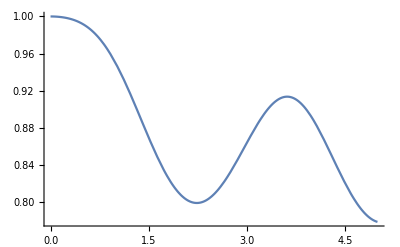

```mathematica
Plot[Evaluate[rb11[t]/.sol],{t,0,5},PlotRange->All]
```

```mathematica
MMAoptpltdata=Flatten@Table[Re@Evaluate[rb11[t]/.sol],{t,0,5,1/100}];
Export["../ipynb/assets/homogen/MMA_optmize_pltdata.txt",MMAoptpltdata]
```

../ipynb/assets/homogen/MMA_optmize_pltdata.txt

Compare data
with
/assets/homogen/optimize_ResultSLSQP240.txt

```mathematica
(*
datar11=Flatten@Import["../ipynb/assets/homogen/optimize_pltdatar11.txt","Table"]
datar11t=Table[i,{i,0,5,1/100}];
Length@data1r11

Length@datar11t

ListPlot[data1r11,Joined->True]
*)
```

### Vacuum Case

Vacuum

```mathematica
Sin[0.4]/2
```

0.194709

```mathematica
(*Clear[hamil,hamilb]*)
hamilv[t_]=delm2E bM ;
%//MatrixForm
hamilvb[t_]=-delm2E bM ;
%//MatrixForm
```

(-0.46053 | 0.194709
0.194709 | 0.46053)

(0.46053 | -0.194709
-0.194709 | -0.46053)

```mathematica
Clear[lhsv,rhsv]
lhsv=I hbar D[rho[t],t]//FullSimplify;
rhsv=hamilv[t].rho[t]-rho[t].hamilv[t]//FullSimplify;
lhsv//MatrixForm;
rhsv//MatrixForm;
-lhsv+rhsv//MatrixForm

Clear[lhsvb,rhsvb]
lhsvb=I hbar D[rhob[t],t]//FullSimplify;
rhsvb=hamilvb[t].rhob[t]-rhob[t].hamilvb[t]//FullSimplify;
lhsvb//MatrixForm;
rhsvb//MatrixForm;
-lhsvb+rhsvb//MatrixForm
```

(0.-0.194709 r12[t]+0.194709 r21[t]-ⅈ r11'[t] | -0.194709 r11[t]-0.921061 r12[t]+0.194709 r22[t]-ⅈ r12'[t]
0.194709 r11[t]+0.921061 r21[t]-0.194709 r22[t]-ⅈ r21'[t] | 0.+0.194709 r12[t]-0.194709 r21[t]-ⅈ r22'[t])

(0.+0.194709 rb12[t]-0.194709 rb21[t]-ⅈ rb11'[t] | 0.194709 rb11[t]+0.921061 rb12[t]-0.194709 rb22[t]-ⅈ rb12'[t]
-0.194709 rb11[t]-0.921061 rb21[t]+0.194709 rb22[t]-ⅈ rb21'[t] | 0.-0.194709 rb12[t]+0.194709 rb21[t]-ⅈ rb22'[t])

```mathematica
hamilv[t]//MatrixForm
hamilvb[t]//MatrixForm
```

(-0.46053 | 0.194709
0.194709 | 0.46053)

(0.46053 | -0.194709
-0.194709 | -0.46053)

```mathematica
hamilv[t].rho[t]-rho[t].hamilv[t]
```

{{0.-0.194709 r12[t]+0.194709 r21[t],-0.194709 r11[t]-0.921061 r12[t]+0.194709 r22[t]},{0.194709 r11[t]+0.921061 r21[t]-0.194709 r22[t],0.+0.194709 r12[t]-0.194709 r21[t]}}

```mathematica
systemvN =Flatten[I hbar D[rho[t],t]-hamilv[t].rho[t]+rho[t].hamilv[t]];
%//MatrixForm
systemvNb = Flatten[I hbar D[rhob[t],t]-hamilvb[t].rhob[t]+rhob[t].hamilvb[t]];
%//MatrixForm
```

(0.+0.194709 r12[t]-0.194709 r21[t]+ⅈ r11'[t]
0.194709 r11[t]+0.921061 r12[t]-0.194709 r22[t]+ⅈ r12'[t]
-0.194709 r11[t]-0.921061 r21[t]+0.194709 r22[t]+ⅈ r21'[t]
0.-0.194709 r12[t]+0.194709 r21[t]+ⅈ r22'[t])

(0.-0.194709 rb12[t]+0.194709 rb21[t]+ⅈ rb11'[t]
-0.194709 rb11[t]-0.921061 rb12[t]+0.194709 rb22[t]+ⅈ rb12'[t]
0.194709 rb11[t]+0.921061 rb21[t]-0.194709 rb22[t]+ⅈ rb21'[t]
0.+0.194709 rb12[t]-0.194709 rb21[t]+ⅈ rb22'[t])

```mathematica
initv={r11[0]==1,r12[0]==0,r21[0]==0,r22[0]==0,rb11[0]==1,rb12[0]==0,rb21[0]==0,rb22[0]==0};
systemv=Flatten@{systemvN,systemvNb};
%//MatrixForm
systemvEqn=Table[systemv[[i]]==0,{i,1,Length@systemv}];
%//MatrixForm
systemvFull=Flatten@{systemvEqn,initv};
%//MatrixForm
```

(0.+0.194709 r12[t]-0.194709 r21[t]+ⅈ r11'[t]
0.194709 r11[t]+0.921061 r12[t]-0.194709 r22[t]+ⅈ r12'[t]
-0.194709 r11[t]-0.921061 r21[t]+0.194709 r22[t]+ⅈ r21'[t]
0.-0.194709 r12[t]+0.194709 r21[t]+ⅈ r22'[t]
0.-0.194709 rb12[t]+0.194709 rb21[t]+ⅈ rb11'[t]
-0.194709 rb11[t]-0.921061 rb12[t]+0.194709 rb22[t]+ⅈ rb12'[t]
0.194709 rb11[t]+0.921061 rb21[t]-0.194709 rb22[t]+ⅈ rb21'[t]
0.+0.194709 rb12[t]-0.194709 rb21[t]+ⅈ rb22'[t])

(0.+0.194709 r12[t]-0.194709 r21[t]+ⅈ r11'[t]==0
0.194709 r11[t]+0.921061 r12[t]-0.194709 r22[t]+ⅈ r12'[t]==0
-0.194709 r11[t]-0.921061 r21[t]+0.194709 r22[t]+ⅈ r21'[t]==0
0.-0.194709 r12[t]+0.194709 r21[t]+ⅈ r22'[t]==0
0.-0.194709 rb12[t]+0.194709 rb21[t]+ⅈ rb11'[t]==0
-0.194709 rb11[t]-0.921061 rb12[t]+0.194709 rb22[t]+ⅈ rb12'[t]==0
0.194709 rb11[t]+0.921061 rb21[t]-0.194709 rb22[t]+ⅈ rb21'[t]==0
0.+0.194709 rb12[t]-0.194709 rb21[t]+ⅈ rb22'[t]==0)

(0.+0.194709 r12[t]-0.194709 r21[t]+ⅈ r11'[t]==0
0.194709 r11[t]+0.921061 r12[t]-0.194709 r22[t]+ⅈ r12'[t]==0
-0.194709 r11[t]-0.921061 r21[t]+0.194709 r22[t]+ⅈ r21'[t]==0
0.-0.194709 r12[t]+0.194709 r21[t]+ⅈ r22'[t]==0
0.-0.194709 rb12[t]+0.194709 rb21[t]+ⅈ rb11'[t]==0
-0.194709 rb11[t]-0.921061 rb12[t]+0.194709 rb22[t]+ⅈ rb12'[t]==0
0.194709 rb11[t]+0.921061 rb21[t]-0.194709 rb22[t]+ⅈ rb21'[t]==0
0.+0.194709 rb12[t]-0.194709 rb21[t]+ⅈ rb22'[t]==0
r11[0]==1
r12[0]==0
r21[0]==0
r22[0]==0
rb11[0]==1
rb12[0]==0
rb21[0]==0
rb22[0]==0)

```mathematica
solv=NDSolve[systemvFull,{r11,r12,r21,r22,rb11,rb12,rb21,rb22},{t,0,20}]
```

{{r11→InterpolatingFunction[{{0., 20.}}, <>],r12→InterpolatingFunction[{{0., 20.}}, <>],r21→InterpolatingFunction[{{0., 20.}}, <>],r22→InterpolatingFunction[{{0., 20.}}, <>],rb11→InterpolatingFunction[{{0., 20.}}, <>],rb12→InterpolatingFunction[{{0., 20.}}, <>],rb21→InterpolatingFunction[{{0., 20.}}, <>],rb22→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
Evaluate[r11[1]/.solv]
```

{0.965144+0. ⅈ}

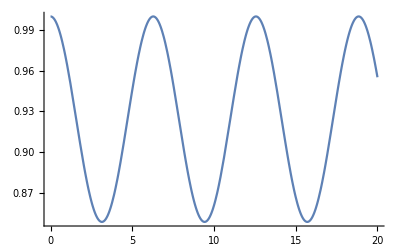

```mathematica
Plot[Evaluate[rb11[t]/.solv],{t,0,20},PlotRange->All]
```

```mathematica
MMAoptpltdataVac=Flatten@Table[Re@Evaluate[rb11[t]/.solv],{t,0,15,1/300}];
Export["../ipynb/assets/homogen/MMA_optmize_Vac_pltdata.txt",MMAoptpltdataVac]
```

../ipynb/assets/homogen/MMA_optmize_Vac_pltdata.txt

### Analytic Stuff

r11[t]->np.sum(initialCondition + ti * v11 * trigf( ti*w11 +u11 ) )

```mathematica
delm2E=1;
analytic=Flatten[I hamilv[t].rho[t]+rho[t].hamilv[t]]/.{r11[t]->initialCondition+ti*v11*trigf[ti*w11+u11],r12[t]->initialCondition+ti*v12*trigf[ti*w12+u12],
r21[t]->initialCondition+ti*v21*trigf[ti*w21+u21],
r22[t]->initialCondition+ti*v22*trigf[ti*w22+u22]};
%//FullSimplify//MatrixForm
Clear[delm2E]
```

((-0.0355353-0.0355353 ⅈ) initialCondition-(0.193649+0.193649 ⅈ) ti v11 trigf[u11+ti w11]+0.158114 ti v12 trigf[u12+ti w12]+(0.+0.158114 ⅈ) ti v21 trigf[u21+ti w21]
(0.351763-0.0355353 ⅈ) initialCondition+0.158114 ti v11 trigf[u11+ti w11]+(0.193649-0.193649 ⅈ) ti v12 trigf[u12+ti w12]+(0.+0.158114 ⅈ) ti v22 trigf[u22+ti w22]
(-0.0355353+0.351763 ⅈ) initialCondition+(0.+0.158114 ⅈ) ti v11 trigf[u11+ti w11]-(0.193649-0.193649 ⅈ) ti v21 trigf[u21+ti w21]+0.158114 ti v22 trigf[u22+ti w22]
(0.351763+0.351763 ⅈ) initialCondition+(0.+0.158114 ⅈ) ti v12 trigf[u12+ti w12]+0.158114 ti v21 trigf[u21+ti w21]+(0.193649+0.193649 ⅈ) ti v22 trigf[u22+ti w22])

```mathematica
D[analytic,w11]
```

{(-0.193649-0.193649 ⅈ) ti^2 v11 trigf'[u11+ti w11],0.158114 ti^2 v11 trigf'[u11+ti w11],(0.+0.158114 ⅈ) ti^2 v11 trigf'[u11+ti w11],0}